```mathematica
2-2
```

0

```mathematica
a_⊗b_:=KroneckerProduct[a,b]
CompConj[A_] := A /.Complex[0,n_]->-Complex[0,n]
Adj[x_]:=CompConj[Transpose[x]]
Brac[a_,b_]:=(Adj[a].b)⟦1⟧⟦1⟧

𝕀=({{1, 0}, {0, 1}});
𝕆=({{0, 0}, {0, 0}});
```

# Logic & Simulation of Hardy's Nonlocality Argument

Nicholas Wheeler
Reed College Physics Department
1 May 2010

```mathematica
Hyperlink["Lucian Hardy","http://www.perimeterinstitute.ca/index.php?option=com_content&task=view&id=30&Itemid=72&pi=1078"]
```

### Introduction

In 1993, Lucian Hardy (PhD 1992) devised a scheme for demonstrating quantum nonlocality ("Nonlocality for two particles without inequalities for almost all entangled states," Phys. Rev. Letters 71, 1665-1668,  (1993)) that Mermin has called "the best version of Bell's theorem." Hardy's scheme resembles Bell's in that it concerns a composite pair of qubits in an entangled state (taken by Bohm/Bell to be the singlet state, but by Hardy to be an adjustably entangled state) and two players—Alice and Bob, each of whom is equipped to examine the state in either of two ways. It differs, however, from Bell's in that in proceeds without reference to any analog of "Bell's inequality" and does not seek statistical evidence of correlation: it places one in position to (in principle) deduce nonlocality from the evidence of a single measurement. In the latter respect it has much in common with the GHZ argument, but is simpler, both conceptually and experimentally (involves only two qubits, not three).

Hardy chose to present his argument as a diabolically clever but seemly unmotivated hat trick (the motivation emerges only retrospectively, at the end of the argument), and to employ a cumbersome notation. For these reasons, I on first reading found his argument difficult to understand. And the efforts of more recent popular expositors—see, for example,

```mathematica
Hyperlink["Dan Styer's Account","http://www.oberlin.edu/physics/dstyer/StrangeQM/Hardy.pdf"]
```

—have (in my view) enjoyed only very limited success. In New Hardy.nb I provide a "computational version" of the material I present on pages 77-85 of Chapter 1 in my Quantum II Notes (2009), but that discussion can be criticized on the ground that it is so encumbered with distracting details (which I now recognize to be largely irrelevant) that it goes only a little way toward clarifying the simple essence of Hardy's argument.

Implications of Hardy's argument were put to experimental test by Paul Kwiat and co-workers (A. G. White, D. F. V. James, P. H. Eberhard & P. G. Kwiat, "Nonmaximally entangled states: production, characterization and utilization," Phys. Rev. Letters 83, 3103-3107 (1999)). A simplified version of Kwiat's experiment was devised by Mark Beck and co-workers (J. A. Carlson, M. D. Olmstead & M. Beck, "Quantum mysteries tested: an experiment implementing Hardy's test of local realism," AJP 74, 180-186 (2006)). Peter Wills has undertaken to reproduce Beck's experiment as a thesis project, and it was that effort that motivated me to revisit the subject, my new objective being to construct a computer simulation of such experiments. 

Yesterday I devised the elementary mathematical lemma that exposes quite clearly the essence of Hardy's argument, and that enables one to proceed efficiently to the results upon which the projected simulation must be based.

### A mathematical lemma

Let p and q be real numbers subject to the contstraint p^2+q^2=1. Then

```mathematica
Subscript[u, 1]=({{p}, {q ⅇ^(ⅈ ϕ)}});
Subscript[u, 2]=({{-q}, {p ⅇ^(ⅈ ϕ)}});
```

are orthogonal unit vectors. Nothing essential to the present discussion will be lost if (for notational simplicity) we assume our orthonormal 2-vectors to be real, of which we will need two pairs:

```mathematica
Subscript[u, 1]=({{p}, {q}});
Subscript[u, 2]=({{-q}, {p}});
Subscript[v, 1]=({{P}, {Q}});
Subscript[v, 2]=({{-Q}, {P}});
```

Construct

```mathematica
Subscript[uu, 1]=Subscript[u, 1]⊗Subscript[u, 1];
Subscript[uu, 2]=Subscript[u, 1]⊗Subscript[u, 2];
Subscript[uu, 3]=Subscript[u, 2]⊗Subscript[u, 1];
Subscript[uu, 4]=Subscript[u, 2]⊗Subscript[u, 2];

Subscript[uv, 1]=Subscript[u, 1]⊗Subscript[v, 1];
Subscript[uv, 2]=Subscript[u, 1]⊗Subscript[v, 2];
Subscript[uv, 3]=Subscript[u, 2]⊗Subscript[v, 1];
Subscript[uv, 4]=Subscript[u, 2]⊗Subscript[v, 2];

Subscript[vu, 1]=Subscript[v, 1]⊗Subscript[u, 1];
Subscript[vu, 2]=Subscript[v, 1]⊗Subscript[u, 2];
Subscript[vu, 3]=Subscript[v, 2]⊗Subscript[u, 1];
Subscript[vu, 4]=Subscript[v, 2]⊗Subscript[u, 2];

Subscript[vv, 1]=Subscript[v, 1]⊗Subscript[v, 1];
Subscript[vv, 2]=Subscript[v, 1]⊗Subscript[v, 2];
Subscript[vv, 3]=Subscript[v, 2]⊗Subscript[v, 1];
Subscript[vv, 4]=Subscript[v, 2]⊗Subscript[v, 2];
```

LEMMA: 4-vectors constructed in this way are orthonormal:

```mathematica
Table[Assuming[{p^2+q^2==1,P^2+Q^2==1}, Simplify[Brac[Subscript[uv, i],Subscript[uv, j]]]],{i,1,4},{j,1,4}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

Similarly (if redundantly)

```mathematica
Table[Assuming[{p^2+q^2==1,P^2+Q^2==1}, Simplify[Brac[Subscript[uu, i],Subscript[uu, j]]]],{i,1,4},{j,1,4}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

So each of those four quartets provides an orthonormal basis in 4-space.

Let

```mathematica
Z=({{Subscript[z, 1]}, {Subscript[z, 2]}, {Subscript[z, 3]
Subscript[z, 4]}})
```

be an arbitrary 4-vector. Its coordinates with respect to (say) the uv-basis are

```mathematica
Table[Brac[Subscript[uv, i],Z],{i,1,4}]//TableForm
```

p P z_1+p Q z_2+P q z_3+q Q z_4
-p Q z_1+p P z_2-q Q z_3+P q z_4
-P q z_1-q Q z_2+p P z_3+p Q z_4
q Q z_1-P q z_2-p Q z_3+p P z_4

```mathematica
Assuming[{p^2+q^2==1,P^2+Q^2==1}, Simplify[∑_(i=1)^4 Subscript[uv, i] Brac[Subscript[uv, i],Z]==Z]]
```

True

The 4-vector Z—which is typically entangled—is displayed here as a superposition of separable/unentangled states.

### Hardy's application of the LEMMA

With

α=Cos[ξ]
β=Sin[ξ]

in mind, Hardy introduces the unit 4-vector

```mathematica
Ψ=α ({{1}, {0}})⊗({{1}, {0}})-β({{0}, {1}})⊗({{0}, {1}});
Ψ//MatrixForm
```

(α
0
0
-β)

to describe a ξ-parameterized population of entangled states of a pair of qubits. The qubits are disentangled if αβ = 0 and maximally entangled (one of the Bell states)if α = β. The "almost all entangled states" to which Hardy alludes in the title of his paper arise when neither of those special conditions is satisfied. 

Hardy imposes two requirements to fix the design of the u and v vectors:

Hardy's first requirement: The coordinates of Ψ with respect to the uu basis are

```mathematica
Assuming[{α^2+β^2.10==1,p^2+q^2==1}, Table[Brac[Subscript[uu, i],Ψ],{i,1,4}]]//TableForm
```

p^2 α-q^2 β
-p q α-p q β
-p q α-p q β
q^2 α-p^2 β

Hardy requires the leading coordinate to vanish:

```mathematica
Assuming[{α^2+β^2.10==1,p^2+q^2==1}, Brac[Subscript[uu, 1],Ψ]]
```

p^2 α-q^2 β

Normalized values of p and q are now determined to within arbitrary ± signs. Setting

p=+(√β)/(√(α + β))
q=-(√α)/(√(α + β))

we have

```mathematica
Table[Subscript[ū, i]=Subscript[u, i]/.{p->(√β)/(√(α + β)),q->-(√α)/(√(α + β))},{i,1,2}];
```

```mathematica
Table[Subscript[OverBar[uu], i]=Subscript[uu, i]/.{p->(√β)/(√(α + β)),q->-(√α)/(√(α + β))},{i,1,4}]
```

{{{β/(α+β)},{-(√α √β)/(α+β)},{-(√α √β)/(α+β)},{α/(α+β)}},{{(√α √β)/(α+β)},{β/(α+β)},{-α/(α+β)},{-(√α √β)/(α+β)}},{{(√α √β)/(α+β)},{-α/(α+β)},{β/(α+β)},{-(√α √β)/(α+β)}},{{α/(α+β)},{(√α √β)/(α+β)},{(√α √β)/(α+β)},{β/(α+β)}}}

```mathematica
Assuming[{α^2+β^2.10==1},Simplify[ Table[Brac[Subscript[OverBar[uu], i],Ψ],{i,1,4}]]]//TableForm
```

0
√α √β
√α √β
α-β

Hardy's second requirement: The coordinates of Ψ with respect to the uv-basis are

```mathematica
Assuming[{α^2+β^2.10==1,p^2+q^2==1,P^2+Q^2==1}, Table[Brac[Subscript[uv, i],Ψ],{i,1,4}]]/.{p->(√β)/(√(α + β)),q->-(√α)/(√(α + β))}//TableForm
```

(P α √β)/(√(α+β))+(Q √α β)/(√(α+β))
-(Q α √β)/(√(α+β))+(P √α β)/(√(α+β))
(P α^(3/2))/(√(α+β))-(Q β^(3/2))/(√(α+β))
-(Q α^(3/2))/(√(α+β))-(P β^(3/2))/(√(α+β))

Hardy requires the final coordinate to vanish. Normalized values of P and Q are now determined to within an arbitrary ± signs. Setting

P=α^(3/2)/(√(α^3+β^3))
Q=-β^(3/2)/(√(α^3+β^3))

we have

```mathematica
Table[Subscript[v̄, i]=Subscript[v, i]/.{P->α^(3/2)/(√(α^3+β^3)),Q->-β^(3/2)/(√(α^3+β^3))},{i,1,2}];
```

```mathematica
Table[Subscript[OverBar[uv], i]=Subscript[uv, i]/.{p->(√β)/(√(α + β)),q->-(√α)/(√(α + β)),P->α^(3/2)/(√(α^3+β^3)),Q->-β^(3/2)/(√(α^3+β^3))},{i,1,4}];
```

```mathematica
Assuming[{α^2+β^2.10==1},Simplify[ Table[Brac[Subscript[OverBar[uv], i],Ψ],{i,1,4}]]]//TableForm
```

(√α √β (α^2-β^2))/(√(α+β) √(α^3+β^3))
(α β √(α+β))/(√(α^3+β^3))
(√(α^3+β^3))/(√(α+β))
0

We have now used up our freedom to assign values to p, q, P and Q. But when we look to the coordinates of Ψ relative to the vu-basis, we find that they are identical to the preceding uv-coordinates, except for interchange of the middle two:

```mathematica
Table[Subscript[OverBar[vu], i]=Subscript[vu, i]/.{p->(√β)/(√(α + β)),q->-(√α)/(√(α + β)),P->α^(3/2)/(√(α^3+β^3)),Q->-β^(3/2)/(√(α^3+β^3))},{i,1,4}];
```

```mathematica
Assuming[{α^2+β^2.10==1},Simplify[ Table[Brac[Subscript[OverBar[vu], i],Ψ],{i,1,4}]]]//TableForm
```

(√α √β (α^2-β^2))/(√(α+β) √(α^3+β^3))
(√(α^3+β^3))/(√(α+β))
(α β √(α+β))/(√(α^3+β^3))
0

Note in particular that the final coordinate again vanishes.

Looking finally to the (enforced) Ψ-coordinates relative to the vv-basis, we have

```mathematica
Table[Subscript[OverBar[vv], i]=Subscript[vv, i]/.{p->(√β)/(√(α + β)),q->-(√α)/(√(α + β)),P->α^(3/2)/(√(α^3+β^3)),Q->-β^(3/2)/(√(α^3+β^3))},{i,1,4}];
```

giving

```mathematica
Assuming[{α^2+β^2==1},Simplify[ Table[Brac[Subscript[OverBar[vv], i],Ψ],{i,1,4}]]]//TableForm
```

(-α+β)/(-1+α β)
(α^(3/2) β^(3/2))/(1-α β)
(α^(3/2) β^(3/2))/(1-α β)
(β (-1+α β+β^2))/(1-α β)

```mathematica
Assuming[{α^2+β^2==1},Simplify[(β(-1+α β+β^2))/(α^2-α β+β^2)==-(α(α-β)β)/(1-α β)]]
```

True

The vv-coordinates of Ψ are relatively complicated, but do entail

```mathematica
Assuming[{α^2+β^2==1},Simplify[∑_(i=1)^4 Brac[Subscript[OverBar[vv], i],Ψ]^2,{i,1,4}]]
```

1

as is required by the fact that Ψ is a unit vector.

Fundamental to Hardy's argument---as will emerge—is the fact that the (square of) the 4th coordinate (which will acquire the interpretation of a probability) almost always does not vanish. Defining

```mathematica
h[ξ_]:=(-(α(α-β)β)/(1-α β))^2/.{α->Cos[ξ],β->Sin[ξ]}
h[ξ]
```

(Cos[ξ]^2 (Cos[ξ]-Sin[ξ])^2 Sin[ξ]^2)/(1-Cos[ξ] Sin[ξ])^2

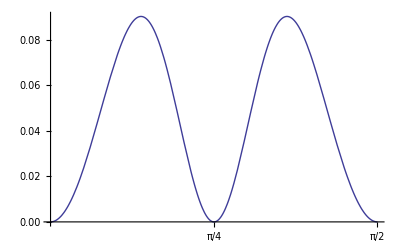

```mathematica
Plot[h[ξ],{ξ,0,π/2},Ticks->{{1/4 π,1/2 π},{}}]
```

Evidently h[ξ] vanishes at ξ=0 and ξ=π/2, where Ψ[ξ] is disentangled, and—curiously—at ξ=π/4, where

Ψ[π/4]=1/(√2)(1
0)⊗(1
0)-1/(√2)(0
1)⊗(0
1)

is maximally entangled (a Bell state). To locate the maxima of h[ξ] we proceed

```mathematica
hprime[ξ_]:=D[h[ξ],ξ]//Simplify
hprime[ξ]
```

(Sin[2 ξ] (-17 Cos[2 ξ]+Cos[6 ξ]+12 Sin[4 ξ]))/(2 (-2+Sin[2 ξ])^3)

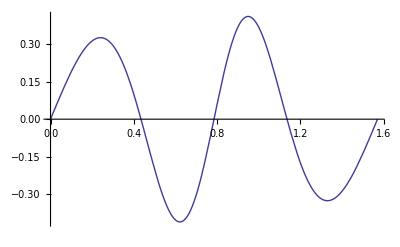

```mathematica
Plot[(Sin[2 ξ] (-17 Cos[2 ξ]+Cos[6 ξ]+12 Sin[4 ξ]))/(2 (-2+Sin[2 ξ])^3),{ξ,.0001,π/2-.0001}]
```

```mathematica
FindRoot[hprime[ξ]==0,{ξ,0.43}]
FindRoot[hprime[ξ]==0,{ξ,1.13}]
```

{ξ→0.434692}

{ξ→1.1361}

```mathematica
h[ξ]/.ξ->0.434692
h[ξ]/.ξ->1.1361
```

0.0901699

0.0901699

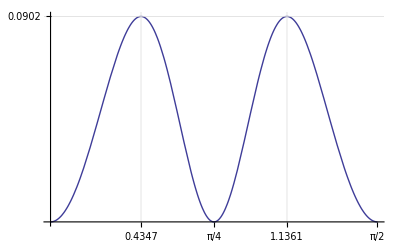

```mathematica
Plot[h[ξ],{ξ,0,π/2},Ticks->{{0.4347,1/4 π,1.1361,1/2 π},{0.0902}}, GridLines->{{0.4347,1.1361},{0.0902}}, AxesLabel->{"ξ"}, PlotStyle->Thick]
```

The intermediately entangled states

```mathematica
Subscript[Ψ, Hardy1]=Cos[0.4347]({{1}, {0}})⊗({{1}, {0}})-Sin[0.4347]({{0}, {1}})⊗({{0}, {1}})//MatrixForm
Subscript[Ψ, Hardy2]=Cos[1.1361]({{1}, {0}})⊗({{1}, {0}})-Sin[1.1361]({{0}, {1}})⊗({{0}, {1}})//MatrixForm
```

(0.906996
0
0
-0.421138)

(0.421135
0
0
-0.906998)

are called "Hardy states."

INTERPOLATED REMARK: Peter Wills, in the thesis which he defended yesterday (5 May), uses a different argument (source not cited) to obtain those same results. The argument is rather pretty, so I reproduce it: from

```mathematica
Assuming[α^2+β^2==1,Simplify[(-(α(α-β)β)/(1-α β))^2]]
```

(α^2 β^2 (1-2 α β))/(-1+α β)^2

we are led to define

```mathematica
f[x_]:=(x^2(1-2x))/(1-x)^2
```

where

```mathematica
x=α β=Cos[ξ]Sin[ξ]
```

ranges on [0, 0.5] as ξ ranges on [0, π/2].  To locate x_max we proceed

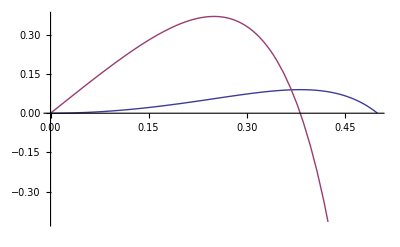

```mathematica
Plot[{f[𝓍],f'[𝓍]},{𝓍,0,1/2}]
```

```mathematica
Solve[f'[x]==0,x]
```

{{x→0},{x→1/2 (3-√5)},{x→1/2 (3+√5)}}

```mathematica
%//N
```

{{x→0.},{x→0.381966},{x→2.61803}}

The command

```mathematica
Solve[Cos[ξ]Sin[ξ]==1/2 (3-√5),ξ];
```

supplies four zeros, of which only the positive two are of interest. They are located at precisey the points obtained previously:

```mathematica
N[{ArcCos[√(1/2+1/2 √(-13+6 √5))],ArcCos[√(1/2 (1-√(-13+6 √5)))]}]
```

{0.434692,1.1361}

Here ends the INTERPOLATED REMARK.

So much for the mathematical underpinnings of Hardy's argument. I turn now to discussion of what this mathematics has to do with the foundations of quantum mechanics—specifically, the quantum mechanics of photons. I preface that discussion with a review of some aspects of the classical physics of (100% polarized monochromatic) light beams.

### Classical light beams and polarizers

REMARK: Here I borrow from the review of Jones Calculus that appears in Quantum Eraser.nb (7 April 2010), where I was borrowing from the discussion that appears on pages 27-37 in my "Ellipsometry: Stokes' parameters & related constructs in optics & classical/quantum mechanics" (1999).

Erect an orthogonal frame in the plane normal to an on-rushing monochromatic optical planewave, and write

ℰ_1 Cos[ω t+δ_1]
ℰ_2 Cos[ω t+δ_2]

to describe the motion of the (transverse) E-field. With R. Clark Jones, fold that information into design of a "Jones vector"—a complex 2-vector

```mathematica
J=({{Subscript[ℰ, 1] ⅇ^(ⅈ Subscript[δ, 1])}, {Subscript[ℰ, 2] ⅇ^(ⅈ Subscript[δ, 2])}});
```

The time-dependent field can then be described

```mathematica
𝒲[t_]:=J*ⅇ^(ⅈ ω t)
𝒲[t]//MatrixForm
```

(ⅇ^(ⅈ t ω+ⅈ δ_1) ℰ_1
ⅇ^(ⅈ t ω+ⅈ δ_2) ℰ_2)

Introduce hermitian matrices by a convention that departs slightly from Pauli's

```mathematica
Subscript[𝕤, 0]=({{1, 0}, {0, 1}});
Subscript[𝕤, 1]=({{1, 0}, {0, -1}});
Subscript[𝕤, 2]=({{0, 1}, {1, 0}});
Subscript[𝕤, 3]=({{0, -ⅈ}, {ⅈ, 0}});
```

Then these simple quadratic constructs

```mathematica
(Adj[J].Subscript[𝕤, 0].J)⟦1⟧⟦1⟧
(Adj[J].Subscript[𝕤, 1].J)⟦1⟧⟦1⟧
(Adj[J].Subscript[𝕤, 2].J)⟦1⟧⟦1⟧/.Subscript[δ, 2]->Subscript[δ, 1]+δ//ExpToTrig
(Adj[J].Subscript[𝕤, 3].J)⟦1⟧⟦1⟧/.Subscript[δ, 2]->Subscript[δ, 1]+δ//ExpToTrig
```

ℰ_1^2+ℰ_2^2

ℰ_1^2-ℰ_2^2

2 Cos[δ] ℰ_1 ℰ_2

2 Sin[δ] ℰ_1 ℰ_2

are recognized to be precisely the parameters (see "Ellipsometry," equation (20) page 12) that Stokes introduced to describe the polarization of such a beam. They possess the great merit that—since interpretable as "intensities"—they are susceptible to direct photometric measurement.

In the following figure I have set

ℰ_1=Cos[θ]
ℰ_2=Sin[θ]

so as to render ℰ_1^2+ℰ_2^2=1 automatic:

```mathematica
Manipulate[ParametricPlot[{Cos[θ]Cos[ t],Sin[θ]Cos[t+δ]},{t,0,2π}, PlotRange->{{-1,1},{-1,1}}, PlotLabel->"Ellipse Traced by Flying E-vector", LabelStyle->{Bold, Red}, Ticks->False, PlotStyle->Thick],{θ,0,π/2},{δ,-π/2,π/2}]
```

Beck restricts his attention—for reasons having to to do with experimental realities—to linearly polarized beams (photons), which result when the relative phase δ = 0 :

```mathematica
Manipulate[ParametricPlot[{Cos[θ]Cos[ t],Sin[θ]Cos[t]},{t,0,2π}, PlotRange->{{-1,1},{-1,1}}, PlotLabel->"Linear Polarization", LabelStyle->{Bold, Red}, Ticks->False, PlotStyle->Thick],{θ,0,π/2}]
```

The Stokes parameters of such beams assume the especially simple form

```mathematica
(Adj[({{Cos[θ]}, {Sin[θ]}})].Subscript[𝕤, 0].({{Cos[θ]}, {Sin[θ]}}))⟦1⟧⟦1⟧//TrigReduce
(Adj[({{Cos[θ]}, {Sin[θ]}})].Subscript[𝕤, 1].({{Cos[θ]}, {Sin[θ]}}))⟦1⟧⟦1⟧//TrigReduce
(Adj[({{Cos[θ]}, {Sin[θ]}})].Subscript[𝕤, 2].({{Cos[θ]}, {Sin[θ]}}))⟦1⟧⟦1⟧//TrigReduce
(Adj[({{Cos[θ]}, {Sin[θ]}})].Subscript[𝕤, 3].({{Cos[θ]}, {Sin[θ]}}))⟦1⟧⟦1⟧
```

1

Cos[2 θ]

Sin[2 θ]

0

Obviously orthogonal to (Cos[θ]
Sin[θ]) is the vector (-Sin[θ]
Cos[θ]). They are seen to refer to beams that are in an obvious sense "oppositely polarized"

```mathematica
Manipulate[ParametricPlot[{{Cos[θ]Cos[ t],Sin[θ]Cos[t]},{-Sin[θ]Cos[ t],Cos[θ]Cos[t]}},{t,0,2π}, PlotRange->{{-1,1},{-1,1}}, PlotLabel->"Opposite Linear Polarization", LabelStyle->{Bold, Red}, Ticks->False, PlotStyle->Thick],{θ,0,π/2}]
```

The adjustment (Cos[θ]
Sin[θ])⟶(-Sin[θ]
Cos[θ]) causes the Stokes parameters (S_1
S_2
S_3) to change sign, which is to say: it sends one point on the (equator of) the Poincaré sphere to go into the diametrically opposite point:

```mathematica
(Adj[({{-Sin[θ]}, {Cos[θ]}})].Subscript[𝕤, 0].({{-Sin[θ]}, {Cos[θ]}}))⟦1⟧⟦1⟧//TrigReduce
(Adj[({{-Sin[θ]}, {Cos[θ]}})].Subscript[𝕤, 1].({{-Sin[θ]}, {Cos[θ]}}))⟦1⟧⟦1⟧//TrigReduce
(Adj[({{-Sin[θ]}, {Cos[θ]}})].Subscript[𝕤, 2].({{-Sin[θ]}, {Cos[θ]}}))⟦1⟧⟦1⟧//TrigReduce
(Adj[({{-Sin[θ]}, {Cos[θ]}})].Subscript[𝕤, 3].({{-Sin[θ]}, {Cos[θ]}}))⟦1⟧⟦1⟧
```

1

-Cos[2 θ]

-Sin[2 θ]

0

Let x and y be real numbers that conform to the normalization condition x^2+y^2=1. Then

```mathematica
X=({{x}, {y ⅇ^(ⅈ ϕ)}});
Y=({{-y}, {x ⅇ^(ⅈ ϕ)}});
```

are Jones vectors that refer to a pair of oppositely polarized beams:

```mathematica
(Adj[X].Y)⟦1⟧⟦1⟧
```

0

(Stokes remarked that such beams do not interfere.) Construct the associated projection matrices

```mathematica
𝕏=X.Adj[X];
𝕐=Y.Adj[Y];
```

which I demonstrate to be projective, orthogonal and complete:

```mathematica
Assuming[x^2+y^2==1,Simplify[𝕏.𝕏-𝕏==𝕆]]
Assuming[x^2+y^2==1,Simplify[𝕐.𝕐-𝕐==𝕆]]
Assuming[x^2+y^2==1,Simplify[𝕏.𝕐==𝕆]]
Assuming[x^2+y^2==1,Simplify[𝕏+𝕐==𝕀]]
```

True

True

True

«1 more identical outputs»

If we define

```mathematica
jx=(Adj[X].J)⟦1⟧⟦1⟧
jy=(Adj[Y].J)⟦1⟧⟦1⟧
```

ⅇ^(ⅈ δ_1) x ℰ_1+ⅇ^(-ⅈ ϕ+ⅈ δ_2) y ℰ_2

-ⅇ^(ⅈ δ_1) y ℰ_1+ⅇ^(-ⅈ ϕ+ⅈ δ_2) x ℰ_2

then we can display an arbitrary J-beam as a weighted superposition of X and Y-beams:

```mathematica
Assuming[x^2+y^2==1,Simplify[J==jx X+jy Y]]
```

True

The intensities of the X and Y-beams are given by expressions

```mathematica
Assuming[x^2+y^2==1,Simplify[ComplexExpand[CompConj[jx]jx]]]
Assuming[x^2+y^2==1,Simplify[ComplexExpand[CompConj[jy]jy]]]
```

x^2 ℰ_1^2+2 x y Cos[ϕ+δ_1-δ_2] ℰ_1 ℰ_2+y^2 ℰ_2^2

y^2 ℰ_1^2-2 x y Cos[ϕ+δ_1-δ_2] ℰ_1 ℰ_2+x^2 ℰ_2^2

that when added give back the intensity of the J-beam:

```mathematica
Assuming[x^2+y^2==1,Simplify[%+%%]]
```

ℰ_1^2+ℰ_2^2

If we assume that the J-beam is linearly polarized, and that so also are the X and Y-beams, then the preceding statements simplify markedly:

```mathematica
jx=(Adj[X].J)⟦1⟧⟦1⟧/.{Subscript[δ, 1]->0,Subscript[δ, 2]->0,ϕ->0}
jy=(Adj[Y].J)⟦1⟧⟦1⟧/.{Subscript[δ, 1]->0,Subscript[δ, 2]->0,ϕ->0}

Expand[Assuming[x^2+y^2==1,Simplify[ComplexExpand[CompConj[jx]jx]/.{Subscript[δ, 1]->0,Subscript[δ, 2]->0,ϕ->0}]]]
Expand[Assuming[x^2+y^2==1,Simplify[ComplexExpand[CompConj[jy]jy]/.{Subscript[δ, 1]->0,Subscript[δ, 2]->0,ϕ->0}]]]
Assuming[x^2+y^2==1,Simplify[%+%%]]
```

x ℰ_1+y ℰ_2

-y ℰ_1+x ℰ_2

x^2 ℰ_1^2+2 x y ℰ_1 ℰ_2+y^2 ℰ_2^2

y^2 ℰ_1^2-2 x y ℰ_1 ℰ_2+x^2 ℰ_2^2

ℰ_1^2+ℰ_2^2

The projection matrices 𝕏 and 𝕐 serve individually to describe the action of crossed polarizers. When a J-beam is incident upon an X-polarizer, its X-component is transmitted and its Y-component is extinguished:

```mathematica
Subscript[J, in]=J;
Subscript[J, out]=𝕏.J;

Subscript[J, in]//MatrixForm
Subscript[J, out]//MatrixForm
```

(ⅇ^(ⅈ δ_1) ℰ_1
ⅇ^(ⅈ δ_2) ℰ_2)

(ⅇ^(ⅈ δ_1) x^2 ℰ_1+ⅇ^(-ⅈ ϕ+ⅈ δ_2) x y ℰ_2
ⅇ^(ⅈ ϕ+ⅈ δ_1) x y ℰ_1+ⅇ^(ⅈ δ_2) y^2 ℰ_2)

The intensity attenuation factor is

```mathematica
Simplify[ComplexExpand[Adj[Subscript[J, out]].Subscript[J, out]]/ComplexExpand[Adj[Subscript[J, in]].Subscript[J, in]]]⟦1⟧⟦1⟧/.x^2+y^2->1
```

(x^2 ℰ_1^2+2 x y Cos[ϕ+δ_1-δ_2] ℰ_1 ℰ_2+y^2 ℰ_2^2)/(ℰ_1^2+ℰ_2^2)

which when the incident beam is linearly polarized and the polarizer is a linear polarizer (the case in which we will acquire primary interest) assumes the simple form.

```mathematica
%/.{Subscript[δ, 1]->0,Subscript[δ, 2]->0,ϕ->0}
```

(x^2 ℰ_1^2+2 x y ℰ_1 ℰ_2+y^2 ℰ_2^2)/(ℰ_1^2+ℰ_2^2)

REMARK: The action of polarizers can be described

```mathematica
Subscript[({{Subscript[S, 0]}, {Subscript[S, 1]}, {Subscript[S, 2]}, {Subscript[S, 3]}}), in]⟶Subscript[({{Subscript[S, 0]}, {Subscript[S, 1]}, {Subscript[S, 2]}, {Subscript[S, 3]}}), out]=𝕄.Subscript[({{Subscript[S, 0]}, {Subscript[S, 1]}, {Subscript[S, 2]}, {Subscript[S, 3]}}), in]
```

where 𝕄 is a 4×4 "Mueller matrix." But I will refrain from pursuit of that elegantly useful topic: for detailed discussion, see "Ellipsometry."

### Photons and meters

The Jones vector

```mathematica
J=({{Subscript[ℰ, 1]}, {Subscript[ℰ, 2] ⅇ^(ⅈ δ)}});
```

—a complex unit vector if, as will be understood,

ℰ_1^2+ℰ_2^2=1

—will be taken now to describe the quantum state of a photon, of which the Stokes parameters continue as before to describe the polarization. The linearly polarized photons to which we will restrict our attention are described by real unit 2-vectors (δ=0).

It is with regard to the action of "polarizers" that the classical and quantum theories differ most markedly. And the differences comes to this: the action of a classical polarizer, as determined by a downstream photometer, is deterministic, while the action of a quantum polarizer—a prototypical "meter"—as determined by a downstream counter, is probabilistic. 

Action of a classical polarizer: Reverting to a notation introduced at the outset, let p and q be a normalized pair of real numbers (marking a point on the unit circle). Then

```mathematica
Subscript[u, 1]=({{p}, {q}});
Subscript[u, 2]=({{-q}, {p}});
```

are orthonormal, and their associated projectors

```mathematica
Subscript[𝕦, 1]=Subscript[u, 1].Adj[Subscript[u, 1]];
Subscript[𝕦, 2]=Subscript[u, 2].Adj[Subscript[u, 2]];
```

are orthogonal and complete. Suppose the Jones vector of a linearly polarized optical beam J has been developed in the u-basis:

```mathematica
Subscript[J, in]=Subscript[j, 1] Subscript[u, 1]+Subscript[j, 2] Subscript[u, 2];
```

where j_1 and j_2 are a normalized pair of real numbers. Presentation of the beam to a 𝕦_1-polarizer produces with certainty the beam

```mathematica
Subscript[J, out1]=Subscript[j, 1] Subscript[u, 1];
```

which has intensity

```mathematica
Assuming[p^2+q^2==1,Simplify[(Adj[Subscript[J, out1]].Subscript[J, out1])⟦1⟧⟦1⟧]]
```

j_1^2

while presentation to a 𝕦_2-polarizer produces (with certainty)

```mathematica
Subscript[J, out2]=Subscript[j, 2] Subscript[u, 2];
```

which has intensity

```mathematica
Assuming[p^2+q^2==1,Simplify[(Adj[Subscript[J, out2]].Subscript[J, out2])⟦1⟧⟦1⟧]]
```

j_2^2

Action of a quantum polarizer: Turning to the analogous quantum mechanical sitution, we begin by incorporating the 𝕦-matrices into the design of matrix that represents the action of a "𝕌-meter"

```mathematica
𝕌=Subscript[𝕦, 1]-Subscript[𝕦, 2];
```

```mathematica
Assuming[p^2+q^2==1,Simplify[Eigenvalues[𝕌]]]
```

{-1,1}

When presented with a photon in state J the meter either announces +1 ("up"), signaling that it prepared a photon in state  u_1 (this it does with probability j_1^2), else it announces "dn", signaling that it prepared a photon in state  u_2 (this it does with probability j_2^2).

In generic quantum contexts it often proves advantageous to employ the density matrix formalism when analyzing the action of meters (when the quantum system is in a mixed state there is no alternative). Look, for example, to the case of a linearly polarized photon: the density matrix

```mathematica
Subscript[ρ, in]=({{Subscript[ℰ, 1]}, {Subscript[ℰ, 2]}}).Adj[({{Subscript[ℰ, 1]}, {Subscript[ℰ, 2]}})];
Subscript[ρ, in]//MatrixForm
```

(ℰ_1^2 | ℰ_1 ℰ_2
ℰ_1 ℰ_2 | ℰ_2^2)

possesses the properties one expects of a pure-state density matrix:

```mathematica
Assuming[Subscript[ℰ, 1]^2+Subscript[ℰ, 2]^2==1,Simplify[Tr[Subscript[ρ, in]]]]
Assuming[Subscript[ℰ, 1]^2+Subscript[ℰ, 2]^2==1,Simplify[Tr[Subscript[ρ, in].Subscript[ρ, in]]]]
```

1

1

The meter announce "up/dn" with probabilities (that yield unity when added)

```mathematica
Subscript[Prob, up]=Assuming[{Subscript[ℰ, 1]^2+Subscript[ℰ, 2]^2==1,p^2+q^2==1},Simplify[Tr[Subscript[ρ, in].Subscript[𝕦, 1]]]]
Subscript[Prob, dn]=Assuming[{Subscript[ℰ, 1]^2+Subscript[ℰ, 2]^2==1,p^2+q^2==1},Simplify[Tr[Subscript[ρ, in].Subscript[𝕦, 2]]]]
Assuming[{Subscript[ℰ, 1]^2+Subscript[ℰ, 2]^2==1,p^2+q^2==1},Simplify[Subscript[Prob, up]+Subscript[Prob, dn]]]
```

(p ℰ_1+q ℰ_2)^2

(q ℰ_1-p ℰ_2)^2

1

The meter-created states are given respectively by

```mathematica
Subscript[ρ, outup]=Assuming[{Subscript[ℰ, 1]^2+Subscript[ℰ, 2]^2==1,p^2+q^2==1},Simplify[(Subscript[𝕦, 1].Subscript[ρ, in].Subscript[𝕦, 1])/Tr[Subscript[ρ, in].Subscript[𝕦, 1]]==Subscript[𝕦, 1]]]
Subscript[ρ, outdn]=Assuming[{p^2+q^2==1,Subscript[j, 1]^2+Subscript[j, 2]^2==1},Simplify[(Subscript[𝕦, 2].Subscript[ρ, in].Subscript[𝕦, 2])/Tr[Subscript[ρ, in].Subscript[𝕦, 2]]==Subscript[𝕦, 2]]]
```

True

True

Such computational labor can, however, be avoided if the input state is presented in "meter pre-adapted form" (as Hardy was at pains to do)

```mathematica
Subscript[J, in]//MatrixForm
```

(p j_1-q j_2
q j_1+p j_2)

```mathematica
Subscript[ρ, in]=Assuming[{Subscript[ℰ, 1]^2+Subscript[ℰ, 2]^2==1,Subscript[j, 1]^2+Subscript[j, 2]^2==1},Simplify[Subscript[J, in].Adj[Subscript[J, in]]]];
Subscript[ρ, in]//MatrixForm
```

((p j_1-q j_2)^2 | (q j_1+p j_2) (p j_1-q j_2)
(q j_1+p j_2) (p j_1-q j_2) | (q j_1+p j_2)^2)

To illustrate the point, I turn to a generic instance of the physical situation contemplated by Hardy:

### Generic entangled pair of photons, meters of two generic designs

Alice has a 𝕦-meter, with eigenstates/projectors

```mathematica
Subscript[u, 1]=({{p}, {q}});
Subscript[u, 2]=({{-q}, {p}});
Subscript[𝕦, 1]=Subscript[u, 1].Adj[Subscript[u, 1]];
Subscript[𝕦, 2]=Subscript[u, 2].Adj[Subscript[u, 2]];
```

Bob has a 𝕧-meter, with

```mathematica
Subscript[v, 1]=({{P}, {Q}});
Subscript[v, 2]=({{-Q}, {P}});
Subscript[𝕧, 1]=Subscript[v, 1].Adj[Subscript[v, 1]];
Subscript[𝕧, 2]=Subscript[v, 2].Adj[Subscript[v, 2]];
```

Alice/Bob's meters are (in God's spectral resolutions) described by the traceless hermitian 4×4 matrices

```mathematica
𝕌=Subscript[𝕦, 1]⊗𝕀-Subscript[𝕦, 2]⊗𝕀;
𝕍=𝕀⊗Subscript[𝕧, 1]-𝕀⊗Subscript[𝕧, 2];
```

```mathematica
𝕌//MatrixForm
𝕍//MatrixForm
```

(p^2-q^2 | 0 | 2 p q | 0
0 | p^2-q^2 | 0 | 2 p q
2 p q | 0 | -p^2+q^2 | 0
0 | 2 p q | 0 | -p^2+q^2)

(P^2-Q^2 | 2 P Q | 0 | 0
2 P Q | -P^2+Q^2 | 0 | 0
0 | 0 | P^2-Q^2 | 2 P Q
0 | 0 | 2 P Q | -P^2+Q^2)

The state vector Ψ of a composite 2-photon system lives in a 4-space, where the 4-vectors

```mathematica
Subscript[uv, 1]=Subscript[u, 1]⊗Subscript[v, 1];
Subscript[uv, 2]=Subscript[u, 1]⊗Subscript[v, 2];
Subscript[uv, 3]=Subscript[u, 2]⊗Subscript[v, 1];
Subscript[uv, 4]=Subscript[u, 2]⊗Subscript[v, 2];
```

provide an orthonormal basis. The associated projectors are

```mathematica
Subscript[𝕦𝕧, 1]=Subscript[uv, 1].Adj[Subscript[uv, 1]];
Subscript[𝕦𝕧, 2]=Subscript[uv, 2].Adj[Subscript[uv, 2]];
Subscript[𝕦𝕧, 3]=Subscript[uv, 3].Adj[Subscript[uv, 3]];
Subscript[𝕦𝕧, 4]=Subscript[uv, 4].Adj[Subscript[uv, 4]];
```

The meter pre-adapted representation of Ψ reads

```mathematica
Ψ=Subscript[ψ, 1] Subscript[uv, 1]+Subscript[ψ, 2] Subscript[uv, 2]+Subscript[ψ, 3] Subscript[uv, 3]+Subscript[ψ, 4] Subscript[uv, 4];
Ψ//MatrixForm
```

(p P ψ_1-p Q ψ_2-P q ψ_3+q Q ψ_4
p Q ψ_1+p P ψ_2-q Q ψ_3-P q ψ_4
P q ψ_1-q Q ψ_2+p P ψ_3-p Q ψ_4
q Q ψ_1+P q ψ_2+p Q ψ_3+p P ψ_4)

where I will, for notational simplicity, assume the coordinates ψ are real. The associated density matrix reads

```mathematica
ρρ=Ψ.Adj[Ψ];
ρρ//MatrixForm
```

((p P ψ_1-p Q ψ_2-P q ψ_3+q Q ψ_4)^2 | (p Q ψ_1+p P ψ_2-q Q ψ_3-P q ψ_4) (p P ψ_1-p Q ψ_2-P q ψ_3+q Q ψ_4) | (P q ψ_1-q Q ψ_2+p P ψ_3-p Q ψ_4) (p P ψ_1-p Q ψ_2-P q ψ_3+q Q ψ_4) | (q Q ψ_1+P q ψ_2+p Q ψ_3+p P ψ_4) (p P ψ_1-p Q ψ_2-P q ψ_3+q Q ψ_4)
(p Q ψ_1+p P ψ_2-q Q ψ_3-P q ψ_4) (p P ψ_1-p Q ψ_2-P q ψ_3+q Q ψ_4) | (p Q ψ_1+p P ψ_2-q Q ψ_3-P q ψ_4)^2 | (p Q ψ_1+p P ψ_2-q Q ψ_3-P q ψ_4) (P q ψ_1-q Q ψ_2+p P ψ_3-p Q ψ_4) | (q Q ψ_1+P q ψ_2+p Q ψ_3+p P ψ_4) (p Q ψ_1+p P ψ_2-q Q ψ_3-P q ψ_4)
(P q ψ_1-q Q ψ_2+p P ψ_3-p Q ψ_4) (p P ψ_1-p Q ψ_2-P q ψ_3+q Q ψ_4) | (p Q ψ_1+p P ψ_2-q Q ψ_3-P q ψ_4) (P q ψ_1-q Q ψ_2+p P ψ_3-p Q ψ_4) | (P q ψ_1-q Q ψ_2+p P ψ_3-p Q ψ_4)^2 | (q Q ψ_1+P q ψ_2+p Q ψ_3+p P ψ_4) (P q ψ_1-q Q ψ_2+p P ψ_3-p Q ψ_4)
(q Q ψ_1+P q ψ_2+p Q ψ_3+p P ψ_4) (p P ψ_1-p Q ψ_2-P q ψ_3+q Q ψ_4) | (q Q ψ_1+P q ψ_2+p Q ψ_3+p P ψ_4) (p Q ψ_1+p P ψ_2-q Q ψ_3-P q ψ_4) | (q Q ψ_1+P q ψ_2+p Q ψ_3+p P ψ_4) (P q ψ_1-q Q ψ_2+p P ψ_3-p Q ψ_4) | (q Q ψ_1+P q ψ_2+p Q ψ_3+p P ψ_4)^2)

Alice makes a measurement, gets "up/dn" with probabilities that I use density matrix formalism to evaluate

```mathematica
Subscript[Prob, Subscript[A, up]]=Assuming[{p^2+q^2==1,P^2+Q^2==1,Subscript[ψ, 1]^2+Subscript[ψ, 2]^2+Subscript[ψ, 3]^2+Subscript[ψ, 4]^2==1},Simplify[Tr[ρρ.(Subscript[𝕦, 1]⊗𝕀)]]];
Subscript[Prob, Subscript[A, dn]]=Assuming[{p^2+q^2==1,P^2+Q^2==1,Subscript[ψ, 1]^2+Subscript[ψ, 2]^2+Subscript[ψ, 3]^2+Subscript[ψ, 4]^2==1},Simplify[Tr[ρρ.(Subscript[𝕦, 2]⊗𝕀)]]];
```

but which, as I demonstrate, can be obtained directly from the "meter pre-adapted" representation of Ψ:

```mathematica
Assuming[{p^2+q^2==1,P^2+Q^2==1,Subscript[ψ, 1]^2+Subscript[ψ, 2]^2+Subscript[ψ, 3]^2+Subscript[ψ, 4]^2==1},Simplify[Subscript[Prob, Subscript[A, up]]==Subscript[ψ, 1]^2+Subscript[ψ, 2]^2]]
Assuming[{p^2+q^2==1,P^2+Q^2==1,Subscript[ψ, 1]^2+Subscript[ψ, 2]^2+Subscript[ψ, 3]^2+Subscript[ψ, 4]^2==1},Simplify[Subscript[Prob, Subscript[A, dn]]==Subscript[ψ, 3]^2+Subscript[ψ, 4]^2]]
```

True

True

The measurement-created states that Alice ships to Bob would, in density matrix formalism, be computed

```mathematica
Subscript[ρρ, Aup]=Assuming[{p^2+q^2==1,P^2+Q^2==1,Subscript[ψ, 1]^2+Subscript[ψ, 2]^2+Subscript[ψ, 3]^2+Subscript[ψ, 4]^2==1},Simplify[((Subscript[𝕦, 1]⊗𝕀).ρρ.(Subscript[𝕦, 1]⊗𝕀))/Tr[ρρ.(Subscript[𝕦, 1]⊗𝕀)]]];
Subscript[ρρ, Adn]=Assuming[{p^2+q^2==1,P^2+Q^2==1,Subscript[ψ, 1]^2+Subscript[ψ, 2]^2+Subscript[ψ, 3]^2+Subscript[ψ, 4]^2==1},Simplify[((Subscript[𝕦, 2]⊗𝕀).ρρ.(Subscript[𝕦, 2]⊗𝕀))/Tr[ρρ.(Subscript[𝕦, 2]⊗𝕀)]]];
```

but become immediately evident if one works from the "meter pre-adapted" representation of Ψ:

```mathematica
Assuming[{p^2+q^2==1,P^2+Q^2==1,Subscript[ψ, 1]^2+Subscript[ψ, 2]^2+Subscript[ψ, 3]^2+Subscript[ψ, 4]^2==1},Simplify[Subscript[ρρ, Aup]==((Subscript[ψ, 1] Subscript[uv, 1]+Subscript[ψ, 2] Subscript[uv, 2]).Adj[(Subscript[ψ, 1] Subscript[uv, 1]+Subscript[ψ, 2] Subscript[uv, 2])])/(Subscript[ψ, 1]^2+Subscript[ψ, 2]^2)]]
Assuming[{p^2+q^2==1,P^2+Q^2==1,Subscript[ψ, 1]^2+Subscript[ψ, 2]^2+Subscript[ψ, 3]^2+Subscript[ψ, 4]^2==1},Simplify[Subscript[ρρ, Adn]==((Subscript[ψ, 3] Subscript[uv, 3]+Subscript[ψ, 4] Subscript[uv, 4]).Adj[(Subscript[ψ, 3] Subscript[uv, 3]+Subscript[ψ, 4] Subscript[uv, 4])])/(Subscript[ψ, 3]^2+Subscript[ψ, 4]^2)]]
```

True

True

Bob will, with his 𝕧-meter, get "up/dn" with conditional probabilities

```mathematica
Subscript[Prob, AupBup]=Assuming[{p^2+q^2==1,P^2+Q^2==1,Subscript[ψ, 1]^2+Subscript[ψ, 2]^2+Subscript[ψ, 3]^2+Subscript[ψ, 4]^2==1},Simplify[Tr[Subscript[ρρ, Aup].(𝕀⊗Subscript[𝕧, 1])]==Subscript[ψ, 1]^2/(Subscript[ψ, 1]^2+Subscript[ψ, 2]^2)]]
Subscript[Prob, AupBdn]=Assuming[{p^2+q^2==1,P^2+Q^2==1,Subscript[ψ, 1]^2+Subscript[ψ, 2]^2+Subscript[ψ, 3]^2+Subscript[ψ, 4]^2==1},Simplify[Tr[Subscript[ρρ, Aup].(𝕀⊗Subscript[𝕧, 2])]==Subscript[ψ, 2]^2/(Subscript[ψ, 1]^2+Subscript[ψ, 2]^2)]]
Subscript[Prob, AdnBup]=Assuming[{p^2+q^2==1,P^2+Q^2==1,Subscript[ψ, 1]^2+Subscript[ψ, 2]^2+Subscript[ψ, 3]^2+Subscript[ψ, 4]^2==1},Simplify[Tr[Subscript[ρρ, Adn].(𝕀⊗Subscript[𝕧, 1])]==Subscript[ψ, 3]^2/(Subscript[ψ, 3]^2+Subscript[ψ, 4]^2)]]
Subscript[Prob, AdnBdn]=Assuming[{p^2+q^2==1,P^2+Q^2==1,Subscript[ψ, 1]^2+Subscript[ψ, 2]^2+Subscript[ψ, 3]^2+Subscript[ψ, 4]^2==1},Simplify[Tr[Subscript[ρρ, Adn].(𝕀⊗Subscript[𝕧, 2])]==Subscript[ψ, 4]^2/(Subscript[ψ, 3]^2+Subscript[ψ, 4]^2)]]
```

True

True

True

«1 more identical outputs»

If, on the other hand, Bob makes the first measurement, his expected results are described by marginal probabilities

```mathematica
Subscript[Prob, Bup]=Subscript[ψ, 1]^2+Subscript[ψ, 3]^2
Subscript[Prob, Bdn]=Subscript[ψ, 2]^2+Subscript[ψ, 4]^2
```

and Alice's expected results are described by the conditional probablities

```mathematica
Subscript[Prob, BupAup]=Subscript[ψ, 1]^2/(Subscript[ψ, 1]^2+Subscript[ψ, 3]^2)
Subscript[Prob, BupAdn]=Subscript[ψ, 3]^2/(Subscript[ψ, 1]^2+Subscript[ψ, 3]^2)
Subscript[Prob, BdnAup]=Subscript[ψ, 2]^2/(Subscript[ψ, 2]^2+Subscript[ψ, 4]^2)
Subscript[Prob, BdnAdn]=Subscript[ψ, 4]^2/(Subscript[ψ, 2]^2+Subscript[ψ, 4]^2)
```

The joint probabilities—computed by appeal to the general formula

joint=marginal*conditional

—are independent of who makes the first measurement, and given very simply by

```mathematica
Subscript[Prob, upup]=Subscript[ψ, 1]^2
Subscript[Prob, updn]=Subscript[ψ, 2]^2
Subscript[Prob, dnup]=Subscript[ψ, 3]^2
Subscript[Prob, dndn]=Subscript[ψ, 4]^2
```

These results make very clear the advantage gained by working from the meter pre-adapted representation of the initial composite state. Which is precisely what Hardy has prepared us to do.

### At last: Hardy's nonlocality argument

A composite pair of photons (one susceptible to measurement by Alice, the other by Bob) are assumed to be initially in the composite state

```mathematica
Ψ=α ({{1}, {0}})⊗({{1}, {0}})-β({{0}, {1}})⊗({{0}, {1}});
Ψ//MatrixForm
```

(α
0
0
-β)

Alice (ditto Bob) possesses both a 𝕦-meter and a 𝕧-meter. Prior to each experiment, Alice and Bob, acting independently, decide which of their respective meters they will use. Four meter-pairs are possible, so four meter pre-adapted representrations of Ψ acquire interest.  If the eigenvectors of  𝕦 and 𝕧 are denoted {u_1,u_2} and {v_1,v_2} then the elements of those pre-adapted bases are

uu_1=u_1⊗u_1;
uu_2=u_1⊗u_2;
uu_3=u_2⊗u_1;
uu_4=u_2⊗u_2;

uv_1=u_1⊗v_1;
uv_2=u_1⊗v_2;
uv_3=u_2⊗v_1;
uv_4=u_2⊗v_2;

vu_1=v_1⊗u_1;
vu_2=v_1⊗u_2;
vu_3=v_2⊗u_1;
vu_4=v_2⊗u_2;

vv_1=v_1⊗v_1;
vv_2=v_1⊗v_2;
vv_3=v_2⊗v_1;
vv_4=v_2⊗v_2;

in terms of which we have

Ψ=A_1 uu_1+A_2 uu_2+A_3 uu_3+A_4 uu_4
Ψ=B_1 uv_1+B_2 uv_2+B_3 uv_3+B_4 uv_4

plus two additional such equations that I refrain for the moment from writing out. Hardy fixes the Ψ-dependent design of 𝕦 (i.e., of  {u_1,u_2}) by imposing the requirement A_1=0. This places him in position to fix the design of 𝕧 (i.e., of  {v_1,v_2}) by imposing the further requirement that B_4=0. At this point he has

Ψ=0 uu_1+A_2 uu_2+A_3 uu_3+A_4 uu_4
Ψ=B_1 uv_1+B_2 uv_2+B_3 uv_3+0 uv_4

from which

Ψ=B_1 vu_1+B_3 vu_2+B_2 vu_3+0 vu_4
Ψ=D_1 vv_1+D_3 vv_2+D_2 vv_3+D_4 vv_4

follow as forced corollaries. (Note that the anticipated C-coefficients are actually a permutation of the B-coefficients—this in consequence of the special structure of Ψ.) Though only the 0s and the fact that D_1≠0 are of relevance to Hardy's argument, they are by now known functions of α and β. We have established that squared coefficients can be read as joint probabilities, and that these are independent of whether it is Alice or Bob who makes the first measurement.  I display those joint probabilities below as functions of ξ:

```mathematica
AProbabilities={0,(√α √β)^2,(√α √β)^2+0.015,(α-β)^2}/.{α->Cos[ξ],β->Sin[ξ]};
BProbabilities={((√α √β (α^2-β^2))/(√(α+β) √(α^3+β^3)))^2,((α β √(α+β))/(√(α^3+β^3)))^2,((√(α^3+β^3))/(√(α+β)))^2,0}/.{α->Cos[ξ],β->Sin[ξ]};
CProbabilities={((√α √β (α^2-β^2))/(√(α+β) √(α^3+β^3)))^2,((√(α^3+β^3))/(√(α+β)))^2,((α β √(α+β))/(√(α^3+β^3)))^2,0}/.{α->Cos[ξ],β->Sin[ξ]};DProbabilities={((-α+β)/(-1+α β))^2,((α^(3/2) β^(3/2))/(1-α β))^2,((α^(3/2) β^(3/2))/(1-α β))^2+0.015,((β (-1+α β+β^2))/(1-α β))^2}/.{α->Cos[ξ],β->Sin[ξ]};
```

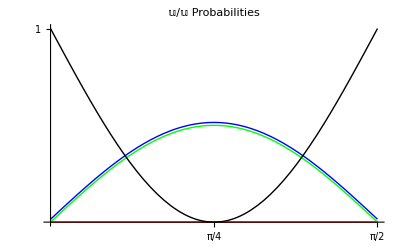

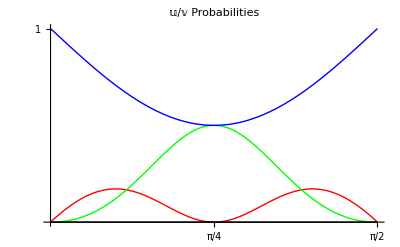

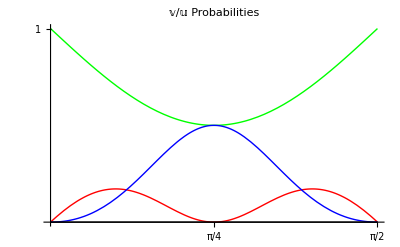

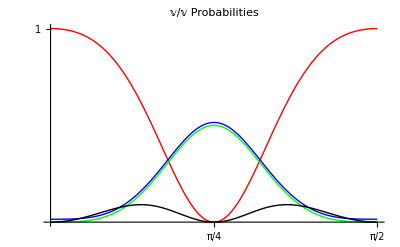

```mathematica
Plot[AProbabilities,{ξ,0,π/2}, Ticks->{{1/4 π,1/2 π},{-1,1}},AxesLabel->{"ξ"}, PlotLabel->"𝕦/𝕦 Probabilities", PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick},{Black,Thick}}]
Plot[BProbabilities,{ξ,0,π/2}, Ticks->{{1/4 π,1/2 π},{-1,1}},AxesLabel->{"ξ"}, PlotLabel->"𝕦/𝕧 Probabilities", PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick},{Black,Thick}}]
Plot[CProbabilities,{ξ,0,π/2}, Ticks->{{1/4 π,1/2 π},{-1,1}},AxesLabel->{"ξ"}, PlotLabel->"𝕧/𝕦 Probabilities", PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick},{Black,Thick}}]
Plot[DProbabilities,{ξ,0,π/2}, Ticks->{{1/4 π,1/2 π},{-1,1}},AxesLabel->{"ξ"}, PlotLabel->"𝕧/𝕧 Probabilities", PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick},{Black,Thick}}]
```

Except for those that vanish identically, all are non-zero except (in some instances) at
ξ = {0, π/4, π/2}. The 0s and 1s that appear at ξ=0 (where α=1 and β=0) can be understood as follows:

A note concerning the edge values of those curves: Those occur at ξ = 0 and ξ = 1, where Ψ is disentangled, so are susceptible to direct analysis. I do so as a check on the accuracy of the results in hand.

At ξ=0 we have

```mathematica
Ψ=up⊗up
```

while from

```mathematica
Subscript[u, 1][α_,β_]:=({{(√β)/(√(α+β))}, {-(√α)/(√(α+β))}})
Subscript[u, 2][α_,β_]:=({{(√α)/(√(α+β))}, {(√β)/(√(α+β))}})
Subscript[v, 1][α_,β_]:=({{(-α^(3/2)+√α β-√β √(α β))/(√(α+β) √(1-α β))}, {(-α √β+β^(3/2)+√α √(α β))/(√(α+β) √(1-α β))}})
Subscript[v, 2][α_,β_]:=({{(α √β-β^(3/2)-√α √(α β))/(√(α+β) √(1-α β))}, {(-α^(3/2)+√α β-√β √(α β))/(√(α+β) √(1-α β))}})
```

we have

```mathematica
Subscript[u, 1][1,0]==-dn
Subscript[u, 2][1,0]==up
Subscript[v, 1][1,0]==-up
Subscript[v, 2][1,0]==-dn
```

True

True

True

«1 more identical outputs»

The equations

Ψ=0 uu_1+A_2 uu_2+A_3 uu_3+A_4 uu_4
Ψ=B_1 uv_1+B_2 uv_2+B_3 uv_3+0 uv_4
Ψ=B_1 vu_1+B_3 vu_2+B_2 vu_3+0 vu_4
Ψ=D_1 vv_1+D_3 vv_2+D_2 vv_3+D_4 vv_4

therefore become

up⊗up=0dn⊗dn-A_2 dn⊗up-A_3 up⊗dn+A_4 up⊗up
up⊗up=B_1 dn⊗up+B_2 dn⊗dn-B_3 up⊗up-0up⊗dn
up⊗up=B_1 up⊗dn-B_3 up⊗up+B_2 dn⊗dn-0dn⊗up
up⊗up=D_1 up⊗up+D_3 up⊗dn+D_2 dn⊗up+D_4 dn⊗dn

which entail

A_4=-B_3=D_1=1

and force all other coefficients to vanish, in precise agreement with the following quotations from the preceding figures:

```mathematica
A4B3C2D1={(α-β)^2,((√(α^3+β^3))/(√(α+β)))^2,((√(α^3+β^3))/(√(α+β)))^2+0.015,((-α+β)/(-1+α β))^2}/.{α->Cos[ξ],β->Sin[ξ]};
```

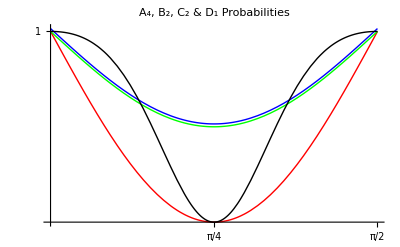

```mathematica
Plot[A4B3C2D1,{ξ,0,π/2}, Ticks->{{1/4 π,1/2 π},{-1,1}},AxesLabel->{"ξ"}, PlotLabel->"A_4, B_2, C_2 & D_1 Probabilities", PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick},{Black,Thick}}]
```

A similar argument accounts for the facts at ξ = 1, where Ψ = -dn⊗dn.

We are in position now to construct the joint, marginal and conditional probabilities that arise in each of the four possible cases:

CASE UU:

From the table of joint probabilities

```mathematica
Subscript[PUU, up,up]=0
Subscript[PUU, up,dn]=Subscript[A, 2]^2
Subscript[PUU, dn,up]=Subscript[A, 3]^2
Subscript[PUU, dn,dn]=Subscript[A, 4]^2
```

(here the first subscript refers to Alice's meter reading, the second to Bob's) we conclude that if Alice/Bob both use 𝕦-meters then if one gets "up" the other necessarily gets "dn" (though it remains a possibility that both get "dn"). Another way to expose this same basic fact: construct the marginal probabilities

```mathematica
Subscript[PUU, Aup]=Subscript[A, 2]^2
Subscript[PUU, Adn]=Subscript[A, 3]^2+Subscript[A, 4]^2

Subscript[PUU, Bup]=Subscript[A, 3]^2
Subscript[PUU, Bdn]=Subscript[A, 2]^2+Subscript[A, 4]^2
```

and use

conditional=joint/marginal

to construct tables of marginal probabilities

```mathematica
Subscript[PUU, Aup|Bup]=0/Subscript[A, 3]^2=0
Subscript[PUU, Aup|Bdn]=Subscript[A, 2]^2/(Subscript[A, 2]^2+Subscript[A, 4]^2)
Subscript[PUU, Adn|Bup]=Subscript[A, 3]^2/Subscript[A, 3]^2=1
Subscript[PUU, Adn|Bdn]=Subscript[A, 4]^2/(Subscript[A, 2]^2+Subscript[A, 4]^2)
```

```mathematica
Subscript[PUU, Bup|Aup]=0/Subscript[A, 2]^2=0
Subscript[PUU, Bup|Adn]=Subscript[A, 3]^2/(Subscript[A, 3]^2+Subscript[A, 4]^2)
Subscript[PUU, Bdn|Aup]=Subscript[A, 2]^2/Subscript[A, 2]^2=1
Subscript[PUU, Bdn|Adn]=Subscript[A, 4]^2/(Subscript[A, 3]^2+Subscript[A, 4]^2)
```

These state quite explicitly if Alice/Bob both use 𝕌-meters, and one gets "up" then the other gets "dn," and vice versa. We are not surprised to discover that in fact

```mathematica
Subscript[PUU, up,dn]=Subscript[A, 2]^2=Subscript[A, 3]^2=Subscript[PUU, dn,up]
```

CASE UV:

From the table of joint probabilities

```mathematica
Subscript[PUV, up,up]=Subscript[B, 1]^2
Subscript[PUV, up,dn]=Subscript[B, 2]^2
Subscript[PUV, dn,up]=Subscript[B, 3]^2
Subscript[PUV, dn,dn]=0
```

we obtain the marginal probabilities

```mathematica
Subscript[PUV, Aup]=Subscript[B, 1]^2+Subscript[B, 2]^2
Subscript[PUV, Adn]=Subscript[B, 3]^2
```

```mathematica
Subscript[PUV, Bup]=Subscript[B, 1]^2+Subscript[B, 3]^2
Subscript[PUV, Bdn]=Subscript[B, 2]^2
```

whence the conditional probabilities

```mathematica
Subscript[PUV, Aup|Bup]=Subscript[B, 1]^2/(Subscript[B, 1]^2+Subscript[B, 3]^2)
Subscript[PUV, Aup|Bdn]=Subscript[B, 2]^2/Subscript[B, 2]^2=1
Subscript[PUV, Adn|Bup]=Subscript[B, 3]^2/(Subscript[B, 1]^2+Subscript[B, 3]^2)
Subscript[PUV, Adn|Bdn]=0/Subscript[B, 2]^2=0
```

```mathematica
Subscript[PUV, Bup|Aup]=Subscript[B, 1]^2/(Subscript[B, 1]^2+Subscript[B, 2]^2)
Subscript[PUV, Bup|Adn]=Subscript[B, 3]^2/Subscript[B, 3]^2=1
Subscript[PUV, Bdn|Aup]=Subscript[B, 2]^2/(Subscript[B, 1]^2+Subscript[B, 2]^2)
Subscript[PUV, Bdn|Adn]=0/Subscript[B, 3]^2=0
```

If Alice uses her 𝕦 meter, and Bob uses his 𝕧 meter, then if Alice gets "dn" then Bob necessarily gets/got "up," and if Bob gets "dn" then Alice necessarily gets/got "up"

CASE VU:

The probabilities here follow from those of CASE UV by B_2^2⇄B_3^2 interchange. Thus

```mathematica
Subscript[PUV, Aup|Bup]=Subscript[B, 1]^2/(Subscript[B, 1]^2+Subscript[B, 2]^2)
Subscript[PUV, Aup|Bdn]=Subscript[B, 3]^2/Subscript[B, 3]^2=1
Subscript[PUV, Adn|Bup]=Subscript[B, 2]^2/(Subscript[B, 1]^2+Subscript[B, 2]^2)
Subscript[PUV, Adn|Bdn]=0/Subscript[B, 2]^2=0
```

```mathematica
Subscript[PUV, Bup|Aup]=Subscript[B, 1]^2/(Subscript[B, 1]^2+Subscript[B, 3]^2)
Subscript[PUV, Bup|Adn]=Subscript[B, 2]^2/Subscript[B, 32]^2=1
Subscript[PUV, Bdn|Aup]=Subscript[B, 3]^2/(Subscript[B, 1]^2+Subscript[B, 3]^2)
Subscript[PUV, Bdn|Adn]=0/Subscript[B, 2]^2=0
```

Once again, Alice/Bob necessarily get opposite meter readings.

The situation thus far can be summarized as follows:

```mathematica
{{U, U}, {up, dn}, {dn, up}}⟹{{U, V}, {up, dn}, {dn, up}} & {{V, U}, {up, dn}, {dn, up}}⟹{{V, V}, {up, dn}, {dn, up}}
```

All of which could be attributed to hidden instruction sets that tell the respective photons how to respond when they encounter a 𝕦/𝕧 meter. Note particularly that the preceding line of argment leads to the conclusion that

V | V
up | up
dn | dn are impossible

But quantum mechanics assigns non-vanishing probabilities to those cases:

CASE VV:

```mathematica
Subscript[PVV, up,up]=Subscript[D, 1]^2
Subscript[PVV, up,dn]=Subscript[D, 2]^2
Subscript[PVV, dn,up]=Subscript[D, 3]^2
Subscript[PVV, dn,dn]=Subscript[D, 4]^2
```

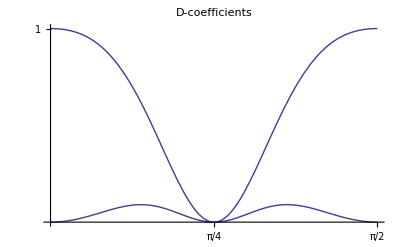

```mathematica
Plot[{((α-β)/(1-α β))^2,((α(α-β)β)/(1-α β))^2}/.{α->Cos[ξ],β->Sin[ξ]},{ξ,0,π/2}, Ticks->{{1/4 π,1/2 π},{-1,1}},AxesLabel->{"ξ"}, PlotLabel->"D-coefficients", PlotStyle->Thick]
```

```mathematica
Assuming[α^2+β^2==1, Simplify[-(β (-1+α β+β^2))/(1-α β)==(α(α-β)β)/(1-α β)]]
```

True